## Лабораторная работа “Одномерная минимизация”.

### Для заданной целевой функции на заданном отрезке (см. конец документа) методом дихотомии и методом золотого сечения найти: 1. Точку минимума (или в некоторых вариантах точку максимума) 2. Минимальное (максимальное) значение целевой функции Методы дихотомии и золотого сечения должны быть реализованы самостоятельно. При поиске точки минимума рассмотреть три варианта с различными значениями параметра точности поиска: ε = 0,01; ε = 0,000001 и ε=10^-17 . Для каждого варианта вывести данные о количестве итераций и количестве вычисленных значений целевой функции. Построить график изменения интервалов неопределенности. Объяснить полученные результаты. Работа должна заканчиваться выводами. Отрезок [a,b] поиска экстремума: [-1,0].

```mathematica
-Graphics- - целевая функция;
```

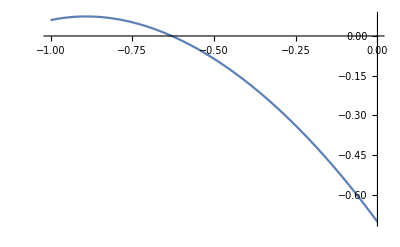

```mathematica
targetFun[x_]:=Block[{},
R1:=Sinh[(√13 x^3-9x-5-√17)/10];
R2:=Tan[(x^2+x+2^(1/3))/(3x-5)];
VarF=R1+R2+0.6;
Return[VarF]];
targetFunArtem[x_]:=ArcTan[(10 x^5-10 √5 x^4+10 x^3+3 x^2-3 √5 x+1)/(2 x^2-2 √5 x+2)]+Cos[(3 x^5-10x+10^(1/3)-2-10 √2)/10];
Plot[targetFun[x],{x,-1,0}]
Plot[targetFunArtem[x],{x,-1,0}];
```

```mathematica
(*funGeorg[x_]:=Log[2*x^5-7 x+Sqrt[11]]+Sinh[(-4 x^2-4 x+3-4 Sqrt[2])/(3 x^2+3 x+3 Sqrt[2])]-1.0;*)
```

```mathematica
Subscript[ϵ, 1]=0.01;
Subscript[ϵ, 2]=0.000001;
Subscript[ϵ, 3]=10^-17;
ϵ=Subscript[ϵ, 3];
```

### Метод дихотомии

```mathematica
iter1=0;
calc1=0;
```

```mathematica
dichmethod[f_,a_,b_]:=Block[{c=a,d=b},
δ=ϵ/3;
l=d-c;
G1=Table[{{"i","x_1","f[x_1]","x_2","f[x_2]","l"}}];
left1={c};
right1={d};
i=0;
While[l>ϵ,
++iter1;
calc1+=2;
Subscript[x, 1]=(c+d)/2-δ;
Subscript[x, 2]=(c+d)/2+δ;
If[f[Subscript[x, 1]]<f[Subscript[x, 2]],c=Subscript[x, 1],d=Subscript[x, 2]];l=d-c;++i;AppendTo[G1,{i,N[Subscript[x, 1]],N[f[Subscript[x, 1]]],N[Subscript[x, 2]],N[f[Subscript[x, 2]]],N[l]}];AppendTo[left1,c]; AppendTo[right1,d]];
SubStar[x]=(c+d)/2;
AppendTo[G1,{i,"x_* = ",N[SubStar[x]],"f[x_*] = ",N[f[SubStar[x]]],""} ];
Print["Точка максимума: ",N[SubStar[x]],"   Значение функции: ",N[f[SubStar[x]]],"   Кол-во итераций: ",iter1,"   Кол-во вычислений: ",calc1]];
```

### Изображения

```mathematica
P1={};
L1={};
R1={};
```

```mathematica
For[i=1,i<Length[right1],++i,Subscript[P1, i]=Plot[i,{x,left1[[i]],right1[[i]]},PlotStyle->Red];AppendTo[P1,Subscript[P1, i]];Subscript[L1, i]=ListLinePlot[{{left1[[i]],i-1},{left1[[i]],i}},PlotStyle->{Dashed,Thickness[0.001]}];
AppendTo[L1,Subscript[L1, i]];
Subscript[R1, i]=ListLinePlot[{{right1[[i]],i-1},{right1[[i]],i}},PlotStyle->{Dashed,Thickness[0.001]}];
AppendTo[R1,Subscript[R1, i]]];
S1=Show[P1,L1,R1,(*ListPlot[{{dichmethod[-1,0],targetFun[dichmethod[-1,0]]}}],*)PlotRange->All,ImageSize->Large,Axes->True,AxesLabel->{"x","i"},AxesStyle->Arrowheads[0.03],GridLines->Automatic,PlotLabel->Style[Framed["Метод дихотомии"],16,Blue,Background->Lighter[Yellow]]];
```

Plot::plld: Endpoints for x in {x,-1,-900719925474099143995200496839339/900719925474099200000000000000000} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot::plld: Endpoints for x in {x,-1,-86469112845513522473539247696576513/86469112845513523200000000000000000} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

### Метод золотого сечения

```mathematica
iter2=0;
calc2=0;
```

```mathematica
goldenmethod[f_,a_,b_]:=Block[{c=a,d=b,l},
l=d-c;
G2=Table[{{"i","x_1","f[x_1]","x_2","f[x_2]","l"}}];
left2={c};
right2={d};
τ=(1+√5)/2;
Subscript[x, 1]=c+l-l/τ;
Subscript[x, 2]=c+l/τ;
Subscript[f, 1]=f[Subscript[x, 1]];
Subscript[f, 2]=f[Subscript[x, 2]];
calc2+=2;
iter2++;
i=0;
While[l>ϵ,
iter2++;
If[f[Subscript[x, 1]]>f[Subscript[x, 2]],{d=Subscript[x, 2],Subscript[x, 2]=Subscript[x, 1],Subscript[x, 1]=c+d-Subscript[x, 2],Subscript[f, 2]=Subscript[f, 1],Subscript[f, 1]=f[Subscript[x, 1]],++calc2},
{c=Subscript[x, 1],Subscript[x, 1]=Subscript[x, 2],Subscript[x, 2]=c+d-Subscript[x, 1],Subscript[f, 1]=Subscript[f, 2],Subscript[f, 2]=f[Subscript[x, 2]],++calc2}];l=d-c;
++i;
AppendTo[G2,{i,N[Subscript[x, 1]],N[f[Subscript[x, 1]]],N[Subscript[x, 2]],N[f[Subscript[x, 2]]],N[l]}];AppendTo[left2,c]; AppendTo[right2,d]];SubStar[x]=(c+d)/2;
AppendTo[G2,{i,"x_* = ",N[SubStar[x]],"f[x_*] = ",N[f[SubStar[x]]],""} ];Print["Точка максимума: ",N[SubStar[x]],"   Значение функции: ",N[f[SubStar[x]]],"   Кол-во итераций: ",iter2,"   Кол-во вычислений: ",calc2]]
```

### Изображения

```mathematica
P2={};
L2={};
R2={};
```

```mathematica
(*For[i=1,i<Length[right2],++i,Subscript[P2, i]=Plot[i,{x,left2[[i]],right2[[i]]},PlotStyle->Red];AppendTo[P2,Subscript[P2, i]];Subscript[L2, i]=ListLinePlot[{{left2[[i]],i-1},{left2[[i]],i}},PlotStyle->{Dashed,Thickness[0.001]}];
AppendTo[L2,Subscript[L2, i]];
Subscript[R2, i]=ListLinePlot[{{right2[[i]],i-1},{right2[[i]],i}},PlotStyle->{Dashed,Thickness[0.001]}];
AppendTo[R2,Subscript[R2, i]]];
S2=Show[P2,L2,R2,(*ListPlot[{{dichmethod[-1,0],targetFun[dichmethod[-1,0]]}}],*)PlotRange->All,ImageSize->Large,Axes->True,AxesLabel->{"x","i"},AxesStyle->Arrowheads[0.03],GridLines->Automatic,PlotLabel->Style[Framed["Метод золотого сечения"],16,Blue,Background->Lighter[Yellow]]];
```

## ___________________________________________________________________________________________ ___________________________________________________________________________________________

Plot::plld: Endpoints for x in {x,-1,-86469112845513522473539247696576513/86469112845513523200000000000000000} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

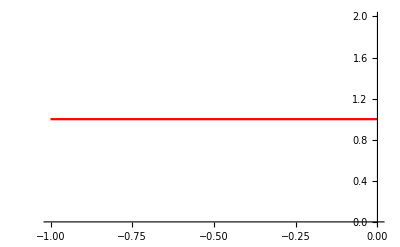
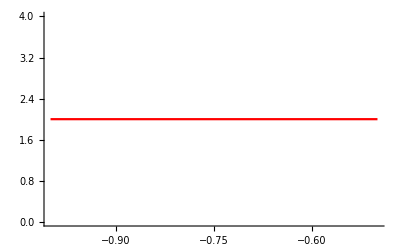
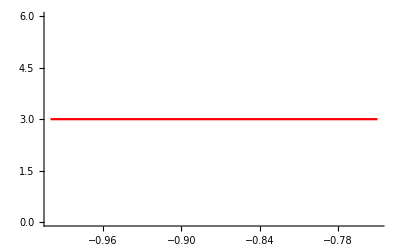
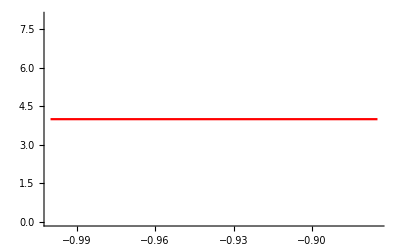
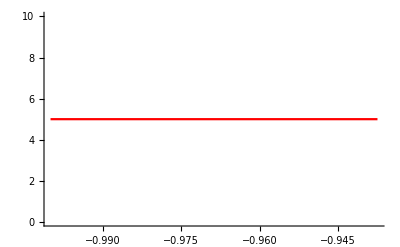
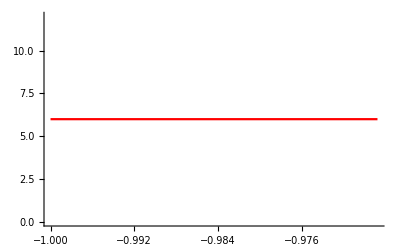
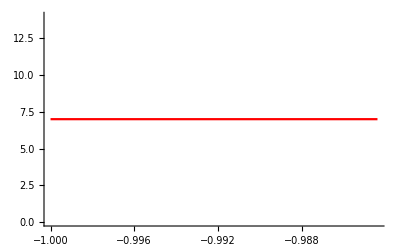
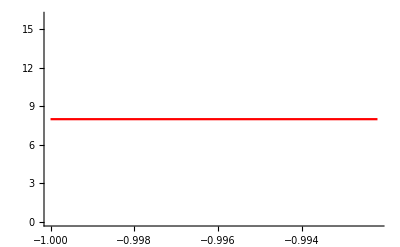
Row[Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Plot[i,{x,left1⟦i⟧,right1⟦i⟧},PlotStyle→Red],Plot[i,{x,left1⟦i⟧,right1⟦i⟧},PlotStyle→Red],Plot[i,{x,left1⟦i⟧,right1⟦i⟧},PlotStyle→Red],Plot[i,{x,left1⟦i⟧,right1⟦i⟧},PlotStyle→Red],Plot[i,{x,left1⟦i⟧,right1⟦i⟧},PlotStyle→Red]},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange→All,ImageSize→Large,Axes→True,AxesLabel→{x,i},AxesStyle→Arrowheads[0.03],GridLines→Automatic,PlotLabel→Метод дихотомии]]

```mathematica
Row[S1]
```

```mathematica
dichmethod[targetFun,-1,0]
```

Точка максимума: -1.   Значение функции: 0.0596289   Кол-во итераций: 59   Кол-во вычислений: 118

```mathematica
(*goldenmethod[targetFun,-1,0]
```

```mathematica
(*Maximize[targetFunArtem[x],x]*)
```

```mathematica
(*Row[Grid[G1,Frame->All],Grid[G2,Frame->All]]*)
```

```mathematica
Grid[Table[{{"","Метод дихотомии (ϵ=0.01)","Метод ЗС (ϵ=0.01)","Метод дихотомии (ϵ=0.000001)","Метод ЗС (ϵ=0.000001)","Метод дихотомии (ϵ=10^-17)","Метод ЗС (ϵ=10^-17)"},{"Точка максимума",-0.8909309895833333,-0.8926091293762095,-0.891180850548347,-0.8911817027837969,"-","-"},{"Значение функции",0.07364702609656815,0.07364475907825394,0.07364709763825428,0.0736470976374447,"-","-"},{"Кол-во итераций",9,10,29,22,"-","-"},{"Кол-во вычислений функции",18,11,44,30,"-","-"}}],Frame->All]
```

| Метод дихотомии (ϵ=0.01) | Метод ЗС (ϵ=0.01) | Метод дихотомии (ϵ=0.000001) | Метод ЗС (ϵ=0.000001) | Метод дихотомии (ϵ=10^-17) | Метод ЗС (ϵ=10^-17)
Точка максимума | -0.890931 | -0.892609 | -0.891181 | -0.891182 | - | -
Значение функции | 0.073647 | 0.0736448 | 0.0736471 | 0.0736471 | - | -
Кол-во итераций | 9 | 10 | 29 | 22 | - | -
Кол-во вычислений функции | 18 | 11 | 44 | 30 | - | -

## Выводы

## В ходе выполнения лабораторной работы были изучены два метода последовательного поиска : «Метод дихотомии» и «Метод золотого сечения» . В обоих методах были получены точка максимума, с заранее заданной точностью, и максимальное значение . Метод дихотомии на каждой итерации вычисляет два значения целевой функции . Метод же золотого сечения каждую итерацию уменьшает исходный интервал в τ ≈ 1.618 ... и вычисляет значение функции один раз за итерацию, кроме первой . Метод золотого сечения является более выгодным (по количеству вычисленных значений функции) .